```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0,0,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0,0,0,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,0,0,0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,0,0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0,0,0,0,0},{0,t,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,t,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,t,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,t,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,t,0},{0,0,0,0,0,0,0,0,0,0,0}}
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,t,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,t,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,t,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,t,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,t}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:=T1[t],T2:=T2[t]},Do[J=Inverse[IdentityMatrix[11]-A.T1.Inverse[IdentityMatrix[11]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

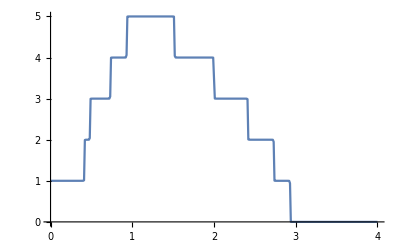
{326.878,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[0,4,0.01]}]]]
```

```mathematica
λ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
λ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
λ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
λ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
λ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
λ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
λ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
(*λ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
(*λ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
(*λ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
(*λ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
(*λ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
(*λ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
(*λ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
(*k714[ω_,ϵ1_]:=k714[ω,ϵ1]=Append[{},Table[λ14[ω,0.001,1,0,ϵ1],{i,400}]];
k713[ω_,ϵ1_]:=k713[ω,ϵ1]=Append[{},Table[λ13[ω,0.001,1,0,ϵ1],{i,400}]];
k712[ω_,ϵ1_]:=k712[ω,ϵ1]=Append[{},Table[λ12[ω,0.001,1,0,ϵ1],{i,400}]];
k711[ω_,ϵ1_]:=k711[ω,ϵ1]=Append[{},Table[λ11[ω,0.001,1,0,ϵ1],{i,400}]];
k710[ω_,ϵ1_]:=k710[ω,ϵ1]=Append[{},Table[λ10[ω,0.001,1,0,ϵ1],{i,400}]];
k79[ω_,ϵ1_]:=k79[ω,ϵ1]=Append[{},Table[λ9[ω,0.001,1,0,ϵ1],{i,400}]];
k78[ω_,ϵ1_]:=k78[ω,ϵ1]=Append[{},Table[λ8[ω,0.001,1,0,ϵ1],{i,400}]];,Mean[k78[ω,ϵ1]],Mean[k79[ω,ϵ1]],Mean[k710[ω,ϵ1]],Mean[k711[ω,ϵ1]],Mean[k713[ω,ϵ1]],Mean[k714[ω,ϵ1]]*)
```

```mathematica
Clear[k77,k76,k75,k74,k73,k72,k71]
```

```mathematica
k77[ω_,ϵ1_]:=k77[ω,ϵ1]=Append[{},Table[λ7[ω,0.001,1,0,ϵ1],{i,100}]];
k76[ω_,ϵ1_]:=k76[ω,ϵ1]=Append[{},Table[λ6[ω,0.001,1,0,ϵ1],{i,100}]];
k75[ω_,ϵ1_]:=k75[ω,ϵ1]=Append[{},Table[λ5[ω,0.001,1,0,ϵ1],{i,100}]];
k74[ω_,ϵ1_]:=k74[ω,ϵ1]=Append[{},Table[λ4[ω,0.001,1,0,ϵ1],{i,100}]];
k73[ω_,ϵ1_]:=k73[ω,ϵ1]=Append[{},Table[λ3[ω,0.001,1,0,ϵ1],{i,100}]];
k72[ω_,ϵ1_]:=k72[ω,ϵ1]=Append[{},Table[λ2[ω,0.001,1,0,ϵ1],{i,100}]];
k71[ω_,ϵ1_]:=k71[ω,ϵ1]=Append[{},Table[λ1[ω,0.001,1,0,ϵ1],{i,100}]]
```

```mathematica
ρ7[ω_,ϵ1_]:=Join[Mean[k71[ω,ϵ1]],Mean[k72[ω,ϵ1]],Mean[k73[ω,ϵ1]],Mean[k74[ω,ϵ1]],Mean[k75[ω,ϵ1]],Mean[k76[ω,ϵ1]],Mean[k77[ω,ϵ1]]]
```

```mathematica
Timing[Mean[ρ7[1.2,0.5]]]
```

{10.5958,4.05741}

```mathematica
Export["7imp3.csv",Table[{ω,Mean[ρ7[ω,0.3]]},{ω,Range[0,4,0.01]}]]
Export["7imp4.csv",Table[{ω,Mean[ρ7[ω,0.4]]},{ω,Range[0,4,0.01]}]]
Export["7imp5.csv",Table[{ω,Mean[ρ7[ω,0.5]]},{ω,Range[0,4,0.01]}]]
Export["7imp6.csv",Table[{ω,Mean[ρ7[ω,0.6]]},{ω,Range[0,4,0.01]}]]
Export["7imp7.csv",Table[{ω,Mean[ρ7[ω,0.7]]},{ω,Range[0,4,0.01]}]]
Export["7imp8.csv",Table[{ω,Mean[ρ7[ω,0.8]]},{ω,Range[0,4,0.01]}]]
Export["7imp9.csv",Table[{ω,Mean[ρ7[ω,0.9]]},{ω,Range[0,4,0.01]}]]
Export["7imp1.csv",Table[{ω,Mean[ρ7[ω,1]]},{ω,Range[0,4,0.01]}]]
```

7imp3.csv

7imp4.csv

7imp5.csv

7imp6.csv

7imp7.csv

7imp8.csv

7imp9.csv

7imp1.csv

```mathematica
μ1=RandomInteger[{1,11}]; μ2=RandomInteger[{1,11}]; μ3=RandomInteger[{1,11}]; μ4=RandomInteger[{1,11}];μ5=RandomInteger[{1,11}]; μ6=RandomInteger[{1,11}]; μ7=RandomInteger[{1,11}]; μ8=RandomInteger[{1,11}]
Print[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

3

89104511103

```mathematica
ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
m1:=m1=Table[{ω,ψ[ω,0.001,1,0,0.5]},{ω,Range[0,4,0.01]}]
```

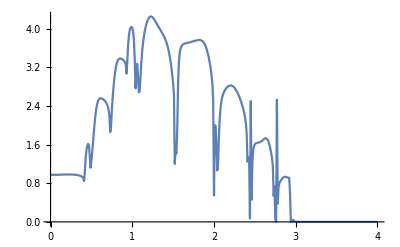

```mathematica
ListLinePlot[m1]
```

```mathematica
ρ73:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/7imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ74:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/7imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ75:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/7imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ76:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/7imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ77:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/7imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ78:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/7imp8.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ79:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/7imp9.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
A7:= {{7,3,ρ73},{7,4,ρ74},{7,5,ρ75},{7,6,ρ76},{7,7,ρ77},{7,8,ρ78},{7,9,ρ79}}
```

```mathematica
A7
```

{{7,3,0.00281312},{7,4,0.00104381},{7,5,0.00055062},{7,6,0.0014542},{7,7,0.00359439},{7,8,0.00664692},{7,9,0.0102237}}

```mathematica
Show[%61,ViewPoint->Front]
```

-Graphics3D-